# Numerical Solution - Gas Electron Multiplier

- Potential

```mathematica
ngasdata= Import["/home/2317101h/year_3/group_project/numerical_sol/section2.2/electricField.dat"];
ngasreshape = ArrayReshape[ngasdata, {100,100}];
```

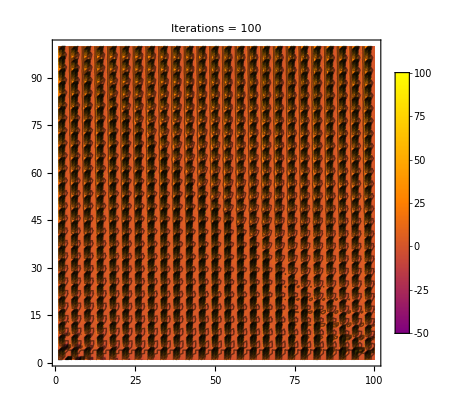

```mathematica
epilog=ListContourPlot[ngasreshape,ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]];
s=ListDensityPlot[ngasreshape,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog,PlotLabel->"Iterations = 100"]
```

```mathematica
Do[Export["/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/pics/"<>ToString[i]<>".png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/" <> ToString[i] <> ".dat"],{100,100}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->ListContourPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/" <> ToString[i] <> ".dat"], {100,100}],ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]],PlotLabel->"Iterations =" <>ToString[i] ]],{i, 0, 9900, 100}]
```

```mathematica
Do[Print[i],{i,1,10}]
```

1

2

3

4

5

6

7

8

9

10

```mathematica
files = FileNames["*.dat", "/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/"];
getData[files_?(VectorQ[#,StringQ]&)]:=Module[{str=ReadList[#,String]&/@files//Flatten},StringCases[str,{"T="~~Whitespace~~x:NumberString:>x,"tts="~~Whitespace~~y:NumberString:>y}]//Flatten//ToExpression//Partition[#,2]&//Mean/@GatherBy[#,First]&];

grabdata[filepath_]:=Module[{text=Import[filepath,"Table"]},Thread[Cases[text,{#,num_}:>ToExpression[num]]&/@{"T=","tts="}]];

grabdata/@files;
```

```mathematica
ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/"  ".dat"],{100,100}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog,PlotLabel->"Iterations =" ]
```

Import::chtype: First argument 100 .dat /home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/ is not a valid file, directory, or URL specification.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed,{100,100}].

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed,{100.,100.}].

ListDensityPlot::arrayerr: ArrayReshape[$Failed,{100.,100.}] must be a valid array.

ListDensityPlot[ArrayReshape[$Failed,{100,100}],PlotTheme→Detailed,1,Epilog→GraphicsComplex[{{1.,1.},{2.,1.},{3.,1.},{4.,1.},{5.,1.},15762,{99.1333,99.1333},{99.1,99.1},{99.0667,99.0667},{99.0333,99.0333}},{1}],PlotLabel→Iterations =]
 |  |  |  |